# Dirichlet Beta Function

### Author

Eric W. Weisstein
February 17, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/SpecialFunctions/DirichletBetaFunction.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/DirichletBetaFunction.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

## Definition

```mathematica
DirichletBeta[x]
```

2^-x (2^-x Zeta[x,1/4]-2^-x Zeta[x,3/4])

#### V6

```mathematica
Sum[(-1)^n(2n+1)^-x,{n,0,∞}]
```

4^-x (Zeta[x,1/4]-Zeta[x,3/4])

```mathematica
Limit[2^(-2 x) (Zeta[x,1/4]-Zeta[x,3/4]),x->1]//FullSimplify
```

π/4

```mathematica
Sum[(-1)^n(2n+1)^(-1),{n,0,∞}]
```

π/4

#### V7

```mathematica
Sum[(-1)^n(2n+1)^-x,{n,0,∞}]
```

2^(-2 x) (Zeta[x,1/4]-Zeta[x,3/4])

```mathematica
Limit[2^(-2 x) (Zeta[x,1/4]-Zeta[x,3/4]),x->1]//FullSimplify
```

π/4

```mathematica
Sum[(-1)^n(2n+1)^(-1),{n,0,∞}]
```

π/4

#### V10

bug(265447)

```mathematica
sum=Sum[(-1)^n(2n+1)^-x,{n,0,∞}]
```

2^(-2 x) (Zeta[x,1/4]-Zeta[x,3/4])

```mathematica
FullSimplify[sum]
```

4^-x (Zeta[x,1/4]-Zeta[x,3/4])

```mathematica
FullSimplify[%-DirichletBeta[x]]
```

0

```mathematica
FunctionExpand[DirichletBeta[x]]
```

2^-x (2^-x Zeta[x,1/4]-2^-x Zeta[x,3/4])

## Plots

```mathematica
<<Utilities`Plot`
<<Utilities`Typesetting`
```

### Real Axis

```mathematica
Plot[DirichletBeta[x],{x,-6,6},AxesLabel->TraditionalForm/@{x,DirichletBeta[x]},
PlotStyle->Red]
```

⁃Graphics⁃

### Complex Plane

```mathematica
ComplexPlot3D[DirichletBeta[z],{z,-2π,2π},PlotPoints->200]//Timing
```

{27.28 Second,⁃GraphicsArray⁃}

```mathematica
ComplexContourPlot[DirichletBeta[z],{z,-2π,2π}]//Timing
```

{66.06 Second,⁃GraphicsArray⁃}

## Special Values

### Negative Odd n

```mathematica
FullSimplify[DirichletBeta[Range[-1,-20,-2]]]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
DirichletBeta[Range[-1,-20,-2]]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Assuming[n∈Integers&&n<0&&Mod[n,2]==1,FullSimplify[FunctionExpand[DirichletBeta[n]]]]
```

0

### Negative Even n

```mathematica
Table[EulerE[-k]/2,{k,-2,-20,-2}]
```

{-1/2,5/2,-61/2,1385/2,-50521/2,2702765/2,-199360981/2,19391512145/2,-2404879675441/2,370371188237525/2}

```mathematica
DirichletBeta[Range[-2,-20,-2]]
```

{-1/2,5/2,-61/2,1385/2,-50521/2,2702765/2,-199360981/2,19391512145/2,-2404879675441/2,370371188237525/2}

```mathematica
Assuming[n∈Integers&&n<0&&Mod[n,2]==0,FullSimplify[FunctionExpand[DirichletBeta[n]]]]
```

EulerE[-n]/2

### Odd positive n

```mathematica
Assuming[n∈Integers&&n>0&&Mod[n,2]==1,FullSimplify[FunctionExpand[DirichletBeta[n]]]]
```

4^-n (Zeta[n,1/4]-Zeta[n,3/4])

```mathematica
Table[((-1)^k EulerE[2k])/(2(2k)!)(π/2)^(2k+1),{k,1,10,2}]
```

{π^3/32,(61 π^7)/184320,(50521 π^11)/14863564800,(199360981 π^15)/5713316492083200,(2404879675441 π^19)/6713375410857443328000}

```mathematica
FullSimplify[DirichletBeta[Range[1,20,2]]]
```

{π/4,π^3/32,(5 π^5)/1536,(61 π^7)/184320,(277 π^9)/8257536,(50521 π^11)/14863564800,(540553 π^13)/1569592442880,(Zeta[15,1/4]-Zeta[15,3/4])/1073741824,(Zeta[17,1/4]-Zeta[17,3/4])/17179869184,(Zeta[19,1/4]-Zeta[19,3/4])/274877906944}

```mathematica
FullSimplify[%]
```

{π/4,π^3/32,(5 π^5)/1536,(61 π^7)/184320,(277 π^9)/8257536,(50521 π^11)/14863564800,(540553 π^13)/1569592442880,(Zeta[15,1/4]-Zeta[15,3/4])/1073741824,(Zeta[17,1/4]-Zeta[17,3/4])/17179869184,(Zeta[19,1/4]-Zeta[19,3/4])/274877906944}

```mathematica
Through[{Numerator,Denominator}[%]]
```

{{1,1,5,61,277,50521,540553,Zeta[15,1/4]-Zeta[15,3/4],Zeta[17,1/4]-Zeta[17,3/4],Zeta[19,1/4]-Zeta[19,3/4]},{4,32,1536,184320,8257536,14863564800,1569592442880,1073741824 π^15,17179869184 π^17,274877906944 π^19}}

### β(1)==π/4

#### Numeric

```mathematica
DirichletBeta[x]/.x->1.00001
```

0.7854

```mathematica
Pi/4.
```

0.785398

#### V6

```mathematica
Limit[DirichletBeta[x],x->1]
```

1/4 (-PolyGamma[0,1/4]+PolyGamma[0,3/4])

```mathematica
FullSimplify[%]
```

π/4

#### V10

```mathematica
DirichletBeta[1]
```

π/4

### β(∞)==1

#### Numeric

```mathematica
DirichletBeta[x]/.x->999.
```

1.

#### v4.2

```mathematica
Limit[DirichletBeta[x],x->Infinity]
```

Limit[4^-x (Zeta[x,1/4]-Zeta[x,3/4]),x→∞]

#### v5.0

```mathematica
Limit[DirichletBeta[x],x->Infinity]
```

Limit[(Zeta[x, 1/4] - Zeta[x, 3/4])/4^x, x -> Infinity]

#### v5.2

```mathematica
Limit[DirichletBeta[x],x->Infinity]
```

Limit[4^-x (Zeta[x,1/4]-Zeta[x,3/4]),x→∞]

#### v6

```mathematica
Limit[DirichletBeta[x],x->Infinity]
```

Limit[4^-x (Zeta[x,1/4]-Zeta[x,3/4]),x→∞]

#### V10

bug(265449)

```mathematica
DirichletBeta[∞]
```

0 (0 Zeta[∞,1/4]+0 Zeta[∞,3/4])

```mathematica
Limit[DirichletBeta[x],x->∞]
```

Limit[2^-x (2^-x Zeta[x,1/4]-2^-x Zeta[x,3/4]),x→∞]

```mathematica
DirichletBeta[100.]
```

1.

### β(n)

#### Old

```mathematica
Beta2[x_]=2^(-x)LerchPhi[-1,x,1/2]
```

2^-x (2^-x Zeta[x,1/4]-2^-x Zeta[x,3/4])

```mathematica
FunctionExpand[FullSimplify[Table[Beta2[n]/.Zeta[x_,nn_,o___]:>Zeta[x,nn],{n,5}]]]
```

∞::indet: Indeterminate expression ComplexInfinity encountered. (More…)

Zeta::nonopt: Options expected (instead of o___) beyond position 2 in Zeta[x_, nn_, o___]. An option must be a rule or a list of rules. (More…)

{Indeterminate,Catalan,π^3/32,1/768 (-8 π^4+PolyGamma[3,1/4]),(5 π^5)/1536}

```mathematica
FullSimplify[1/768 (-8 π^4+PolyGamma[3,1/4])-(PolyGamma[3,1/4]-PolyGamma[3,3/4])/1536]
```

0

```mathematica
FullSimplify[FunctionExpand[Table[DirichletBeta[n],{n,1,10}]]]
```

∞::indet: Indeterminate expression ComplexInfinity encountered. (More…)

{Indeterminate,Catalan,π^3/32,(PolyGamma[3,1/4]-PolyGamma[3,3/4])/1536,(5 π^5)/1536,(PolyGamma[5,1/4]-PolyGamma[5,3/4])/491520,(61 π^7)/184320,(PolyGamma[7,1/4]-PolyGamma[7,3/4])/330301440,(277 π^9)/8257536,(PolyGamma[9,1/4]-PolyGamma[9,3/4])/380507258880}

```mathematica
v2=Table[(-1)^k EulerE[2k](Pi/2)^(2k+1)/2/
(2k)!,{k,0,5}]
```

{π/4,π^3/32,(5 π^5)/1536,(61 π^7)/184320,(277 π^9)/8257536,(50521 π^11)/14863564800}

#### V10

```mathematica
Table[DirichletBeta[n],{n,4}]//FullSimplify
```

{π/4,Catalan,π^3/32,1/256 (Zeta[4,1/4]-Zeta[4,3/4])}

## Sums

```mathematica
<<Utilities`Simplify`
```

```mathematica
Sum[Log[((4k+1)^(1/(4k+1)^n))/((4k-1)^(1/(4k-1)^n))],{k,∞}]
```

∑_k^∞ Log[(-1+4 k)^(-(-1+4 k)^-n) (1+4 k)^((1+4 k)^-n)]

```mathematica
FullSimplify[-D[2^(-2 x) (Zeta[x,1/4]-Zeta[x,3/4]),x]/.x->n,n∈Integers&&n>0]
```

4^-n (Log[4] (Zeta[n,1/4]-Zeta[n,3/4])-Zeta^(1,0)[n,1/4]+Zeta^(1,0)[n,3/4])

### ∑_(k=1)^∞ log((4 k+1)^(1/(4 k+1))/(4 k-1)^(1/(4 k-1)))==-β'(1)

#### V6

```mathematica
Sum[Log[(4k+1)^(1/(4k+1))/(4k-1)^(1/(4k-1))],{k,∞}]//Expand
```

∑_(k=1)^∞ Log[(-1+4 k)^(-1/(-1+4 k)) (1+4 k)^(1/(1+4 k))]

```mathematica
Total[N[Table[Log[(4k+1)^(1/(4k+1))/(4k-1)^(1/(4k-1))],{k,10^4}]]]
```

-0.192769

```mathematica
1/4 π (log((2 π Gamma[3/4]^2)/Gamma[1/4]^2)+ℽ)//N
```

0.192901

#### V7

```mathematica
Sum[Log[(4k+1)^(1/(4k+1))/(4k-1)^(1/(4k-1))],{k,∞}]//GammaSimplify//LogExpand
```

-1/4 π (EulerGamma+2 Log[2]+3 Log[π]-4 Log[Gamma[1/4]])

### ∑_(k=1)^∞ log(((4 k+1)^(1/(4 k+1)^2))/((4 k-1)^(1/(4 k-1)^2)))==-β'(2)

```mathematica
Sum[Log[((4k+1)^(1/(4k+1)^2))/((4k-1)^(1/(4k-1)^2))],{k,∞}]//Expand
```

```mathematica
Sum[Log[((4k+1)^(1/(4k+1)^2))/((4k-1)^(1/(4k-1)^2))],{k,∞}]//Expand
```

2 Catalan Log[2]-1/16 Zeta^(1,0)[2,1/4]+1/16 Zeta^(1,0)[2,3/4]

```mathematica
-Derivative[1][DirichletBeta][2]//FullSimplify//LogExpand//Expand
```

2 Catalan Log[2]-1/16 Zeta^(1,0)[2,1/4]+1/16 Zeta^(1,0)[2,3/4]

### ∑_(k=1)^∞ log(((4 k+1)^(1/(4 k+1)^3))/((4 k-1)^(1/(4 k-1)^3)))==-β'(3)

```mathematica
Sum[Log[((4k+1)^(1/(4k+1)^3))/((4k-1)^(1/(4k-1)^3))],{k,∞}]
```

1/64 (4 π^3 Log[2]-Zeta^(1,0)[3,1/4]+Zeta^(1,0)[3,3/4])

```mathematica
-Derivative[1][DirichletBeta][3]//FullSimplify//LogExpand
```

1/64 (4 π^3 Log[2]-Zeta^(1,0)[3,1/4]+Zeta^(1,0)[3,3/4])

### ∑_(k=1)^∞ log(((4 k+1)^(1/(4 k+1)^4))/((4 k-1)^(1/(4 k-1)^4)))==-β'(4)

```mathematica
Sum[Log[((4k+1)^(1/(4k+1)^4))/((4k-1)^(1/(4k-1)^4))],{k,∞}]
```

1/64 (4 π^3 Log[2]-Zeta^(1,0)[3,1/4]+Zeta^(1,0)[3,3/4])

```mathematica
-Derivative[1][DirichletBeta][3]//FullSimplify//LogExpand
```

1/64 (4 π^3 Log[2]-Zeta^(1,0)[3,1/4]+Zeta^(1,0)[3,3/4])

## Derivatives

### Directly

```mathematica
FunctionExpand[Derivative[1][DirichletBeta][x]]
```

-4^-x Log[4] Zeta[x,1/4]+4^-x Log[4] Zeta[x,3/4]+4^-x Zeta^(1,0)[x,1/4]-4^-x Zeta^(1,0)[x,3/4]

### Via Sum

```mathematica
D[(-1)^n(2n+1)^-x,x]
```

-(-1)^n (1+2 n)^-x Log[1+2 n]

```mathematica
Sum[-(-1)^n (1+2 n)^-x Log[1+2 n],{n,0,∞}]
```

∑_(n=0)^∞ -(-1)^n (1+2 n)^-x Log[1+2 n]

### β'(-1)

#### Old

```mathematica
Derivative[1][DirichletBeta][-1]
```

-4 Log[4] (Zeta[-1,1/4]-Zeta[-1,3/4])+4 (-1/96+Catalan/(4 π)+Log[Glaisher]/8-Zeta^(1,0)[-1,3/4])

```mathematica
FullSimplify[%]
```

(2 Catalan)/π

```mathematica
N[%,10]
```

0.583121808

#### V10

```mathematica
Derivative[1][DirichletBeta][-1]
```

-2 Log[2] (2 Zeta[-1,1/4]-2 Zeta[-1,3/4])+2 (2 (-1/96+Catalan/(4 π)+Log[Glaisher]/8)-2 Log[2] Zeta[-1,1/4]+2 Log[2] Zeta[-1,3/4]-2 Zeta^(1,0)[-1,3/4])

```mathematica
FullSimplify[%]
```

(2 Catalan)/π

### β'(0)

#### Old

```mathematica
Derivative[1][DirichletBeta][0]
```

-Log[4]/2+Zeta^(1,0)[0,1/4]-Zeta^(1,0)[0,3/4]

```mathematica
%//FullSimplify
```

Log[(2 Gamma[5/4])/Gamma[3/4]]

```mathematica
<<Utilities`Simplify`
```

```mathematica
GammaSimplify[Log[(2 Gamma[5/4])/Gamma[3/4]]]
```

Log[Gamma[1/4]^2/(2 √2 π)]

```mathematica
N[%,20]
```

0.39159439270683677647

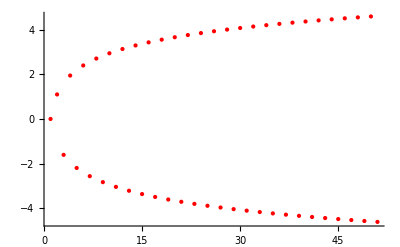

```mathematica
ListPlot[Table[-(-1)^n Log[1+2 n],{n,0,50}],PlotStyle->{Red,Thickness[.02]}]
```

#### V6

```mathematica
Sum[-(-1)^n Log[1+2 n],{n,0,∞}]
```

Sum::div: Sum does not converge.

∑_(n=0)^∞ -(-1)^n Log[1+2 n]

#### V7

```mathematica
-(-1)^n (1+2 n)^-x Log[1+2 n]/.x->0
```

-(-1)^n Log[1+2 n]

```mathematica
Sum[-(-1)^n Log[1+2 n],{n,0,∞}]
```

Sum::div: Sum does not converge.

∑_(n=0)^∞ -(-1)^n Log[1+2 n]

```mathematica
NSum[-(-1)^n Log[1+2 n],{n,0,∞}]
```

SequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

0.391594

```mathematica
Sum[-(-1)^n Log[1+2 n],{n,0,10^4}]//N
```

-4.5602

#### V10

```mathematica
Derivative[1][DirichletBeta][0]
```

-Log[2]+Zeta^(1,0)[0,1/4]-Zeta^(1,0)[0,3/4]

```mathematica
FullSimplify[%]
```

Log[(2 Gamma[5/4])/Gamma[3/4]]

### β'(1)==1/4 π (log((2 π (Γ(3/4))^2)/(Γ(1/4))^2)+ℽ)

#### Old

```mathematica
Derivative[1][DirichletBeta][1]
```

∞::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered. More…

Indeterminate

```mathematica
Derivative[1][DirichletBeta][1.+10^-10]
```

0.1929

```mathematica
N[1/4 π (EulerGamma+Log[(2 π Gamma[3/4]^2)/Gamma[1/4]^2])]
```

0.192901

#### v5.2

```mathematica
l=Limit[Derivative[1][DirichletBeta][x],x->1]
```

Limit[-4^-x Log[4] (Zeta[x,1/4]-Zeta[x,3/4])+4^-x (Zeta^(1,0)[x,1/4]-Zeta^(1,0)[x,3/4]),x→1]

#### v6

```mathematica
Limit[Derivative[1][DirichletBeta][x],x->1]
```

Limit[-4^-x Log[4] (Zeta[x,1/4]-Zeta[x,3/4])+4^-x (Zeta^(1,0)[x,1/4]-Zeta^(1,0)[x,3/4]),x→1]

#### V10

bug(265453)

```mathematica
Derivative[1][DirichletBeta][1]
```

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[Derivative[1][DirichletBeta][x],x->1]
```

1/4 (Log[4] (PolyGamma[0,1/4]-PolyGamma[0,3/4])-StieltjesGamma[1,1/4]+StieltjesGamma[1,3/4])

```mathematica
FullSimplify[%]
```

1/4 (-π Log[4]-StieltjesGamma[1,1/4]+StieltjesGamma[1,3/4])

```mathematica
FunctionExpand[%]
```

1/4 (-π Log[4]-StieltjesGamma[1,1/4]+StieltjesGamma[1,3/4])

```mathematica
N[%]
```

0.192901

```mathematica
1/4 Pi(EulerGamma+2Log[2]+3Log[π]-4Log[Gamma[1/4]])//N
```

0.192901

### β'(1-2n)

Benoit Cloitre <abmt@wanadoo.fr>
Wed, 25 Jan 2006 15:03:03 -0600

```mathematica
Derivative[1][DirichletBeta][1-2n]//FullSimplify
```

4^(-1+2 n) (Log[4] (-Zeta[1-2 n,1/4]+Zeta[1-2 n,3/4])+Zeta^(1,0)[1-2 n,1/4]-Zeta^(1,0)[1-2 n,3/4])

```mathematica
Table[Derivative[1][DirichletBeta][1-2n],{n,1}]//FullSimplify
```

{(2 Catalan)/π}

```mathematica
Table[(n+1/2)EulerE[2n] DirichletBeta[2n]/DirichletBeta[2n-1],{n,1}]//FullSimplify
```

{-(6 Catalan)/π}

...not quite right...

```mathematica
N[%]
```

{-1.74937,12.758,-214.042,6234.34}

### β''(1)

#### v5.2

```mathematica
Limit[Derivative[1][DirichletBeta][x],x->1]//InputForm
```

Limit[-((Log[4]*(Zeta[x, 1/4] - Zeta[x, 3/4]))/4^x) + 
  (Derivative[1, 0][Zeta][x, 1/4] - Derivative[1, 0][Zeta][x, 3/4])/4^x, x -> 1]

```mathematica
l=Limit[Derivative[2][DirichletBeta][x],x->1]
```

Limit[4^-x Log[4]^2 (Zeta[x,1/4]-Zeta[x,3/4])-2 4^-x Log[4] (Zeta^(1,0)[x,1/4]-Zeta^(1,0)[x,3/4])+4^-x (Zeta^(2,0)[x,1/4]-Zeta^(2,0)[x,3/4]),x→1]

#### v6

```mathematica
l=Limit[Derivative[2][DirichletBeta][x],x->1]
```

1/4 (-Log[4]^2 PolyGamma[0,1/4]+Log[4]^2 PolyGamma[0,3/4]-2 Log[4] Zeta^(1,0)[1,1/4]+Log[16] Zeta^(1,0)[1,3/4]+Zeta^(2,0)[1,1/4]-Zeta^(2,0)[1,3/4])

```mathematica
FullSimplify[FunctionExpand[l]]
```

1/4 (-π Log[4] (2 EulerGamma+Log[(16 π^2 Gamma[3/4]^4)/Gamma[1/4]^4])+Zeta^(2,0)[1,1/4]-Zeta^(2,0)[1,3/4])

```mathematica
GammaSimplify[FullSimplify[FunctionExpand[l]]]
```

1/4 (-π Log[4] (2 EulerGamma+Log[(64 π^6)/Gamma[1/4]^8])+Zeta^(2,0)[1,1/4]-Zeta^(2,0)[1,3/4])

#### V10

```mathematica
Derivative[2][DirichletBeta][1]
```

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate

```mathematica
Limit[Derivative[2][DirichletBeta][x],x->1]
```

1/4 (-4 Log[2]^2 (PolyGamma[0,1/4]-PolyGamma[0,3/4])+Log[16] (StieltjesGamma[1,1/4]-StieltjesGamma[1,3/4])+StieltjesGamma[2,1/4]-StieltjesGamma[2,3/4])

```mathematica
FullSimplify[%]
```

1/4 (4 π Log[2]^2+Log[16] (StieltjesGamma[1,1/4]-StieltjesGamma[1,3/4])+StieltjesGamma[2,1/4]-StieltjesGamma[2,3/4])

```mathematica
FunctionExpand[%]
```

1/4 (4 π Log[2]^2+Log[16] (StieltjesGamma[1,1/4]-StieltjesGamma[1,3/4])+StieltjesGamma[2,1/4]-StieltjesGamma[2,3/4])

```mathematica
N[%]
```

-0.154142